# COVID19

#### Atualizado 08/05/2020

### A Curva de Gompertz

f(t)=a e^(-b e^(-c t))
No limite de t→∞ temos um valor fixo de "a"
e a meia altura "a/2" ocorre em t=-(ln(ln(2)/b))/c
Podemos rescrever como,

```mathematica
Gompertz[A_,M_,τ_,t_]:=A Exp[-Exp[(M-t)/τ]];
```

onde N0 é a população inicial, Ninf é a populaçao final e b é taxa de cresciemnto inicial

veja mais em https://en.wikipedia.org/wiki/Gompertz_function

## Mineração dos dados

Pagina com os dados da COVID curado pela Johns Hopkins University no GitHub, https://github.com/CSSEGISandData/COVID-19

### Casos Confirmados

```mathematica
confirmed=Import["https://raw.githubusercontent.com/CSSEGISandData/COVID-19/master/csse_covid_19_data/csse_covid_19_time_series/time_series_covid19_confirmed_global.csv"];
posBR=Position[confirmed[[All,2]],"Brazil"][[1,1]];
Dias=DateList[{#,{"Month","Day","YearShort"}}]&/@Drop[confirmed[[1]],4];
DadosBRConfirmados=Transpose[{Dias,Drop[confirmed[[posBR]],4]}];
```

### Casos com Mortes

```mathematica
Fatalidades=Import["https://raw.githubusercontent.com/CSSEGISandData/COVID-19/master/csse_covid_19_data/csse_covid_19_time_series/time_series_covid19_deaths_global.csv"];
posBR=Position[Fatalidades[[All,2]],"Brazil"][[1,1]];
Dias=DateList[{#,{"Month","Day","YearShort"}}]&/@Drop[Fatalidades[[1]],4];
DadosBRFatalidades=Transpose[{Dias,Drop[Fatalidades[[posBR]],4]}];
```

### Casos Recuperados

```mathematica
Recuperados=Import["https://raw.githubusercontent.com/CSSEGISandData/COVID-19/master/csse_covid_19_data/csse_covid_19_time_series/time_series_covid19_recovered_global.csv"];posBR=Position[Recuperados[[All,2]],"Brazil"][[1,1]];
Dias=DateList[{#,{"Month","Day","YearShort"}}]&/@Drop[Recuperados[[1]],4];
DadosBRRecuperados=Transpose[{Dias,Drop[Recuperados[[posBR]],4]}];
```

## Mortes Brasil

#### Segmentar da série historica apenas os dados acima de uma fatalidade

```mathematica
len=Length[DadosBRFatalidades[[All,2]]];
DadosBR=Select[Transpose[{Range[len],DadosBRFatalidades[[All,2]]}],#[[2]]>1&];
```

#### Definie a função de Gompertz e ajusta

```mathematica
Gompertz[A_,M_,τ_,t_]:=A Exp[-Exp[(M-t)/τ]];
BRnml=NonlinearModelFit[DadosBR,Gompertz[A,M,τ,t],{{A,40000},{τ,25},{M,100}},t,Weights->1/DadosBR[[All,2]]]//Quiet;
```

#### Ver os dados do ajuste e calcular a banda de incerteza de 95%

```mathematica
BRnml["ParameterTable"]
bandsBR95[x_]=BRnml["MeanPredictionBands",ConfidenceLevel->.95];
```

| Estimate | Standard Error | t-Statistic | P-Value
A | 40126.8 | 4011.58 | 10.0027 | 2.51035×10^-13
τ | 29.651 | 1.06376 | 27.8737 | 2.6741×10^-31
M | 119.342 | 2.22405 | 53.6597 | 1.64767×10^-44

#### Identifica quantos dias para atingir a metade do total de mortes, e uma estimativa destas mortes

```mathematica
dias=Round[((M-τ Log[Log[2]])/.BRnml["BestFitParameters"])-DadosBR[[-1,1]]]
Round[A/.BRnml["BestFitParameters"],100]
Round[BRnml["ParameterErrors"][[1]],100]
text=Graphics[Text[Style[ToString[Round[A/.BRnml["BestFitParameters"],100]]<> "±"<>ToString[Round[BRnml["ParameterErrors"][[1]],100]]<>" mortes\n daqui a "<>ToString[IntegerPart[dias]]<> " dias.",16,Bold],{DadosBR[[1,1]]+2,Max[DadosBR[[All,2]]]/2},{-1,0}]];
```

23

40100

4000

#### Gráfico dos resultados

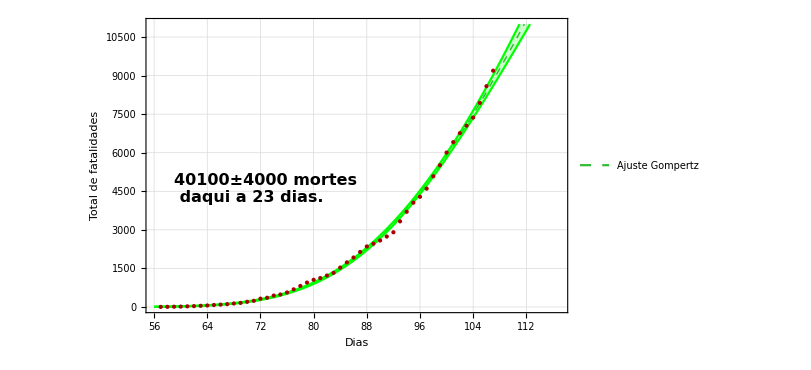

```mathematica
Show[Plot[{BRnml[t],bandsBR95[t]},{t,DadosBR[[All,1]][[1]]-1,DadosBR[[All,1]][[-1]]+10},Filling->{2->{1}},PlotStyle->{{Darker[Green],Thick,Dashed,Opacity[0.8]},Green},PlotLegends->Placed[{"Ajuste Gompertz",None} ,{Left,Top}],PlotTheme->"Detailed",FrameLabel->{{"Total de fatalidades",None},{"Dias", "Brasil "<>DateString[{"Day", "/","Month","/","YearShort"}]}},LabelStyle->Directive[Black,FontFamily->"Helvetica",FontSize->24],FrameStyle->Directive[Black,Thick],ImageSize->500,PlotStyle->Directive[Blue,Thick,PointSize[Large],"LineOpacity"->0.8],PlotRange->{All,{0,Round[DadosBR[[-1,2]]+2000,500]}}],ListPlot[DadosBR,PlotTheme->"Detailed",FrameLabel->{{"Total de fatalidades",None},{"Dias","Brasil"}},LabelStyle->Directive[Black,FontFamily->"Helvetica",FontSize->20],FrameStyle->Directive[Black,Thick],ImageSize->500,PlotStyle->Directive[Darker[Red],Thick,PointSize[Large]],Joined->False,PlotRange->All],text,ImageSize->600]
```